```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

```mathematica
A=197;
r0=6.38;(*fm*)
R=3 r0;(*fm*)
a0=0.535 ;(*fm*)
ρ0=1/NIntegrate[4π r^2 1/(1+Exp[(r-r0)/a0]),{r,0,∞}];
ws[r_]:=ρ0/(1+Exp[(r-r0)/a0]);
```

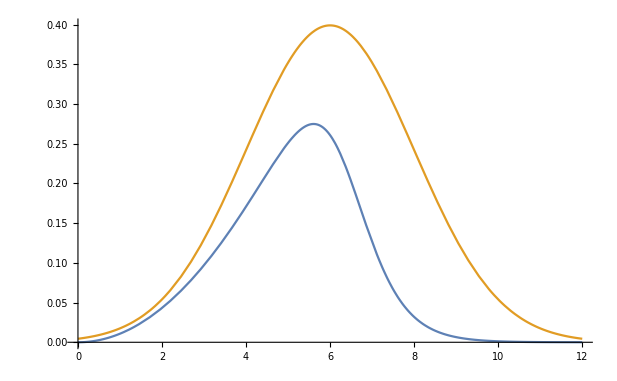

```mathematica
Plot[{4π r^2 ws[r],2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]},{r,0,12}]
```

388

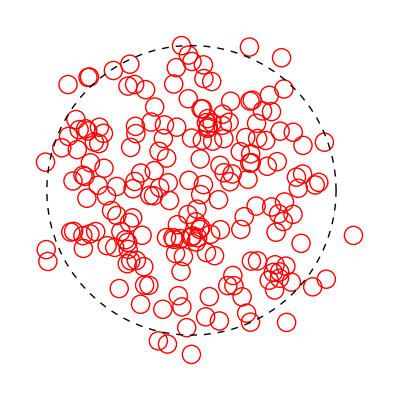

```mathematica
coords={};
SetSharedVariable[coords];
Module[{r,θ,i=0,rM,ϕ},While[Length[coords]<A,rM=RandomVariate[NormalDistribution[6,2]];
r=RandomReal[]R ;
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π rM^2 ws[rM]/(2 1/(√(2π 2^2))Exp[(-(rM-6)^2)/(2 2^2)]) ,coords=Append[coords,{rM,θ,ϕ}]];i++];Print[i]];
Graphics[{Table[{Red,Circle[{coords[[i,1]]Cos[coords[[i,3]]]Sin[coords[[i,2]]],coords[[i,1]]Sin[coords[[i,3]]]Sin[coords[[i,2]]]},0.4]},{i,1,A,1}],{Dashed,Circle[{0,0},r0]}}]
```

```mathematica
σ=4.2;(*fm^2=mb/10, at √s=200GeV*)
d=√(σ/π);
```

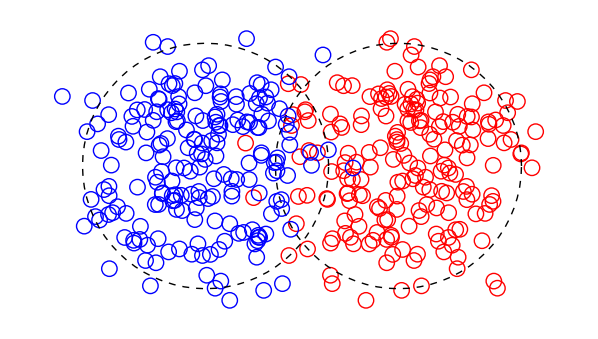

56

```mathematica
b=10;
coords1={};
Module[{r,θ,ϕ,i=0,rM},While[Length[coords1]<A,rM=RandomVariate[NormalDistribution[6,2]];
r=RandomReal[]R ;
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π rM^2 ws[rM]/(2 1/(√(2π 2^2))Exp[(-(rM-6)^2)/(2 2^2)]) ,coords1=Append[coords1,{rM,θ,ϕ}]];i++];]
coords2={};
Module[{r,θ,ϕ,i=0,rM},While[Length[coords2]<A,rM=RandomVariate[NormalDistribution[6,2]];
r=RandomReal[]R ;
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]< 4π rM^2 ws[rM]/(2 1/(√(2π 2^2))Exp[(-(rM-6)^2)/(2 2^2)]) ,coords2=Append[coords2,{rM,θ,ϕ}]];i++];]
coords1=coords1/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]+b/2,a Sin[phi]Sin[th]};
coords2=coords2/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]-b/2,a Sin[phi]Sin[th]};
Graphics[{Table[{Red,Circle[{coords1[[i,1]],coords1[[i,2]]},0.4]},{i,1,A,1}],{Dashed,Circle[{b/2,0},r0]},Table[{Blue,Circle[{coords2[[i,1]],coords1[[i,2]]},0.4]},{i,1,A,1}],{Dashed,Circle[{-b/2,0},r0]}}]
Ncoll=0;
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,Ncoll=Ncoll+1;],{ii,1,A},{i,1,A}];
Ncoll
```

```mathematica
glauberNcoll[impact_]:=Module[{b=impact,coords1={},coords2={},Ncoll=0,r,θ,ϕ,i=0},
While[Length[coords1]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]) ,coords1=Append[coords1,{r,θ,ϕ}]];i++];
While[Length[coords2]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]) ,coords2=Append[coords2,{r,θ,ϕ}]];i++];
coords1=coords1/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]+b/2,a Sin[phi]Sin[th]};
coords2=coords2/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]-b/2,a Sin[phi]Sin[th]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,Ncoll=Ncoll+1;],{ii,1,A},{i,1,A}];
Return[Ncoll]]
```

```mathematica
bmax=12;
bNcollTab=ParallelTable[{impact,glauberNcoll[impact]},{impact,0,bmax,0.5},{i,0,100}];//AbsoluteTiming
```

{199.884,Null}

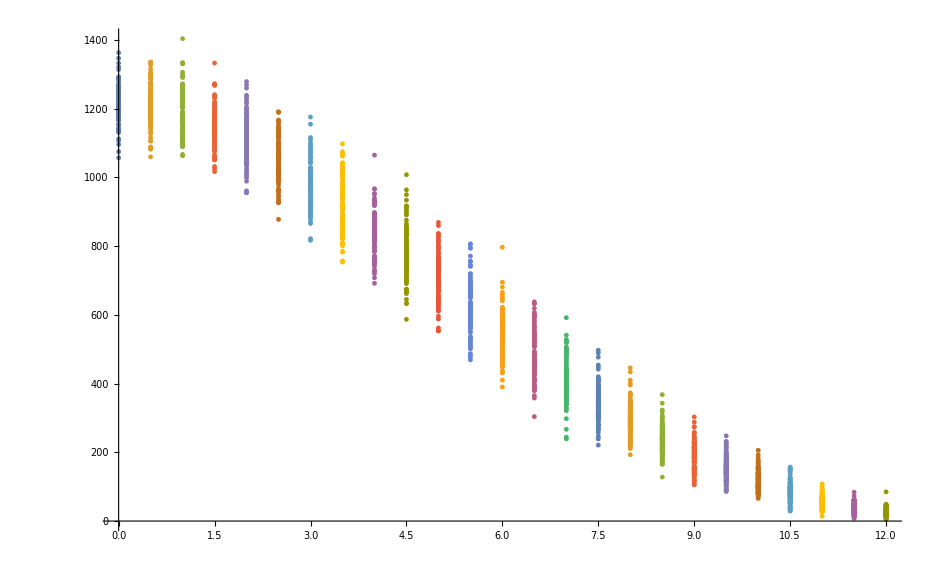

```mathematica
ListPlot[bNcollTab,PlotRange->All]
```

```mathematica
bNcollmeanTab=Table[{b,0.},{b,0,12,0.5}];
Do[bNcollmeanTab[[i,2]]=Mean[bNcollTab[[i,All,2]]],{i,Length[bNcollTab]}]
```

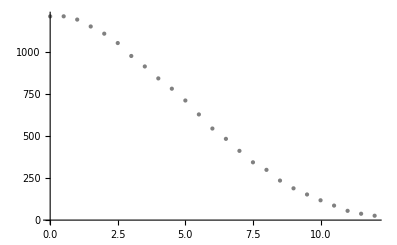

```mathematica
ListPlot[bNcollmeanTab,PlotStyle->{PointSize[Large],Gray}]
```

```mathematica
glauberNpart[impact_]:=Module[{b=impact,coords1={},coords2={},r,θ,ϕ,i=0,collindex1={},collindex2={}},
While[Length[coords1]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]) ,coords1=Append[coords1,{r,θ,ϕ}]];i++];
While[Length[coords2]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]) ,coords2=Append[coords2,{r,θ,ϕ}]];i++];
coords1=coords1/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]+b/2,a Sin[phi]Sin[th]};
coords2=coords2/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]-b/2,a Sin[phi]Sin[th]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,collindex1=Append[collindex1,i];collindex2=Append[collindex2,ii]],{ii,1,A},{i,1,A}];
Return[Length[DeleteDuplicates[collindex1]]+Length[DeleteDuplicates[collindex2]]]]
```

```mathematica
bmax=15;
bNpartTab=ParallelTable[{impact,glauberNpart[impact]},{impact,0,bmax,0.5},{i,0,100}];//AbsoluteTiming
```

{205.942,Null}

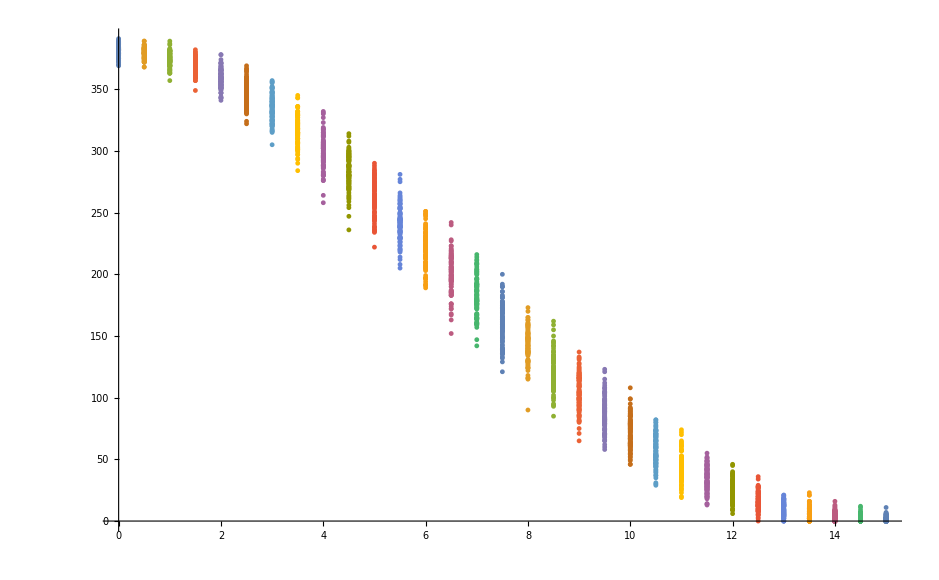

```mathematica
ListPlot[bNpartTab,PlotRange->All]
```

```mathematica
bNpartmeanTab=Table[{b,0.},{b,0,12,0.5}];
Do[bNpartmeanTab[[i,2]]=Mean[bNpartTab[[i,All,2]]],{i,Length[bNpartTab]}]
```

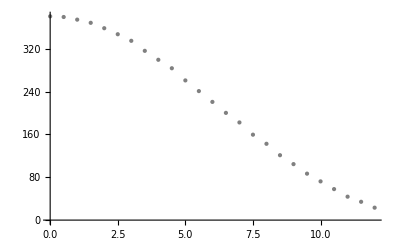

```mathematica
ListPlot[bNpartmeanTab,PlotStyle->{PointSize[Large],Gray}]
```

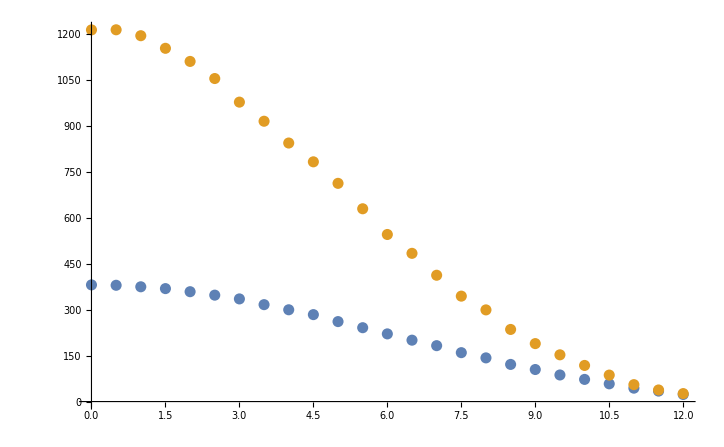

```mathematica
ListPlot[{bNpartmeanTab,bNcollmeanTab},PlotRange->All]
```

```mathematica
NpartOptical={{0.,378.80202013894785},{0.1,378.74275037928555},{0.2,378.5649960720415},{0.30000000000000004,378.2686674707589},{0.4,377.85367676414194},{0.5,377.31997907423755},{0.6000000000000001,376.6675215081528},{0.7000000000000001,375.89484424706717},{0.8,375.00641220844653},{0.9,373.9980254968526},{1.,372.87146851866305},{1.1,371.6272257471181},{1.2000000000000002,370.2659679304428},{1.3,368.7885706940277},{1.4000000000000001,367.19614083671155},{1.5,365.48997853463453},{1.6,363.67158786520156},{1.7000000000000002,361.74279123219117},{1.8,359.70553177410284},{1.9000000000000001,357.56198390206094},{2.,355.3144958695577},{2.5,342.61093602026347},{3.,327.73432102020575},{3.5,311.072608104606},{4.,293.00446209464786},{4.5,273.87843714721964},{5.,254.00758757005136},{5.5,233.67196332357815},{6.,213.12379695983495},{6.5,192.5927564338881},{7.,172.29064320020822},{7.5,152.41484688972653},{8.,133.15165601286435},{8.5,114.67785756309947},{9.,97.16259819099758},{9.5,80.76840574308231},{10.,65.6516213482929},{10.5,51.96178319495709},{11.,39.83881745149888},{11.5,29.405698605817204},{12.,20.752621870686372},{12.1,19.2396833429672},{12.2,17.799281233019943},{12.299999999999999,16.43108667404205},{12.4,15.134587943399504},{12.5,13.909082256594612},{12.6,12.753665998235322},{12.7,11.667229078807425},{12.799999999999999,10.648452423715687},{12.9,9.695808064427082},{13.,8.807563740248126},{13.1,7.981790629086733},{13.2,7.216375757506756},{13.3,6.509036951982307},{13.4,5.857343790000809},{13.5,5.258737989817142},{13.6,4.710559055637524},{13.7,4.2100704567365765},{13.8,3.754486503550584},{13.9,3.3410003736514646},{14.,2.966809500191921},{14.1,2.6291419146723105},{14.2,2.3252788846718038},{14.3,2.052576041698857},{14.4,1.8084935745609756},{14.5,1.590561890082674},{14.6,1.3964678198442182},{14.7,1.2240140075969694},{14.8,1.0711374270733847},{14.9,0.935912645979184},{15.,0.8165528008662291}};
NcollOptical={{0.,1232.0782068474368},{0.1,1231.7727293662679},{0.2,1230.859248630568},{0.30000000000000004,1229.3386569542204},{0.4,1227.2155649277813},{0.5,1224.4956988493504},{0.6000000000000001,1221.185953020914},{0.7000000000000001,1217.294603586564},{0.8,1212.832115207291},{0.9,1207.8092678349913},{1.,1202.238228862369},{1.1,1196.1321187254832},{1.2000000000000002,1189.5049484646072},{1.3,1182.3714562196678},{1.4000000000000001,1174.7470086231804},{1.5,1166.6474675684287},{1.6,1158.0891393984596},{1.7000000000000002,1149.088244453213},{1.8,1139.662457418436},{1.9000000000000001,1129.8277607758616},{2.,1119.601459955785},{2.5,1063.1837623551726},{3.,999.4462822237391},{3.5,930.2875456738652},{4.,857.4141961610048},{4.5,782.3454721982777},{5.,706.4333006373408},{5.5,630.8844469104865},{6.,556.7788753645875},{6.5,485.08301346420575},{7.,416.6582246498473},{7.5,352.26493297270605},{8.,292.56292626589556},{8.5,238.10838992992421},{9.,189.34661779832138},{9.5,146.60038072256222},{10.,110.05322312692432},{10.5,79.7263677205611},{11.,55.45098982143411},{11.5,36.84167803967844},{12.,23.285562392691173},{12.1,21.11191641400607},{12.2,19.10094228671289},{12.299999999999999,17.24516597367502},{12.4,15.536984960002032},{12.5,13.968712284558952},{12.6,12.532619589983497},{12.7,11.22098489486877},{12.799999999999999,10.026133803137336},{12.9,8.940488584932988},{13.,7.956607630442673},{13.1,7.067227005158699},{13.2,6.265296729113328},{13.3,5.544014114306378},{13.4,4.8968511388349585},{13.5,4.317579551363419},{13.6,3.8002880587053993},{13.7,3.339396333171773},{13.8,2.929664006867539},{13.9,2.5661941773571413},{14.,2.244433315438448},{14.1,1.9601669103319692},{14.2,1.7095118500762858},{14.3,1.4889056001144176},{14.4,1.2950935511342154},{14.5,1.1251139376664634},{14.6,0.9762880146890299},{14.7,0.8461778932752313},{14.8,0.7326064041851661},{14.9,0.6336143477405426},{15.,0.5474491077535242}};
```

```mathematica
NcollOpticalinter=Interpolation[NcollOptical];
NpartOpticalinter=Interpolation[NpartOptical];
```

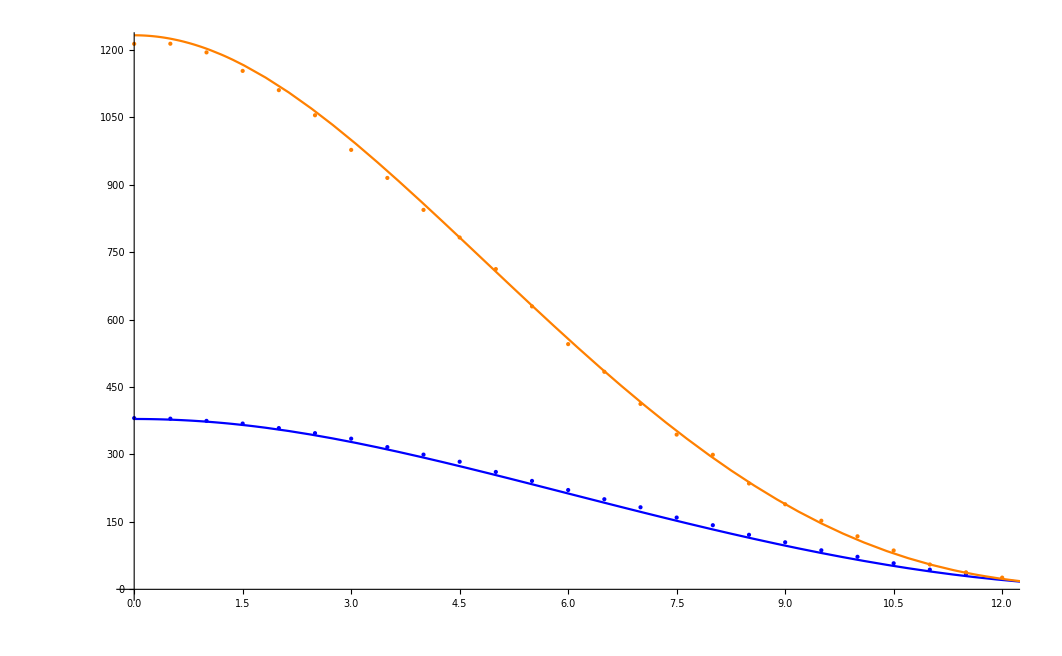

```mathematica
Show[ListPlot[{bNpartmeanTab,bNcollmeanTab},PlotRange->All,PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Orange}}],Plot[{NpartOpticalinter[x],NcollOpticalinter[x]},{x,0,15},PlotStyle->{{Blue},{Orange}}]]
```

```mathematica
glauberMCcollcoords[impact_]:=Module[{b=impact,coords1={},coords2={},r,θ,ϕ,i=0,collcoords={}},
While[Length[coords1]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]) ,coords1=Append[coords1,{r,θ,ϕ}]];i++];
While[Length[coords2]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)]) ,coords2=Append[coords2,{r,θ,ϕ}]];i++];
coords1=coords1/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]+b/2,a Sin[phi]Sin[th]};
coords2=coords2/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]-b/2,a Sin[phi]Sin[th]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,collcoords=Append[Append[collcoords,coords1[[i]]],coords2[[i]]];],{ii,1,A},{i,1,A}];
Return[collcoords]];
```

```mathematica
ecc[collcoords_,n_]:=Module[{cent=collcoords/.{a_,b_}:>{a-Mean[collcoords[[All,1]]],b-Mean[collcoords[[All,2]]]},centpol=ConstantArray[0,Length[collcoords]]},
centpol=cent/.{a_,b_}:>CoordinateTransformData["Cartesian"->"Polar","Mapping",{a,b}];
Return[(√(Mean[Table[centpol[[i,1]]^2 Cos[n centpol[[i,2]]],{i,Length[centpol]}]]^2+Mean[Table[centpol[[i,1]]^2 Sin[n centpol[[i,2]]],{i,Length[centpol]}]]^2))/Mean[Table[centpol[[i,1]]^2,{i,Length[centpol]}]]]];
```

```mathematica
data=ParallelTable[{b,Table[ecc[glauberMCcollcoords[b],2],{i,0,10}]},{b,0,12,0.5}];//AbsoluteTiming
```

{164.057,Null}

```mathematica
data=data/.{a_,b_}:>{a,Mean[b]};
```

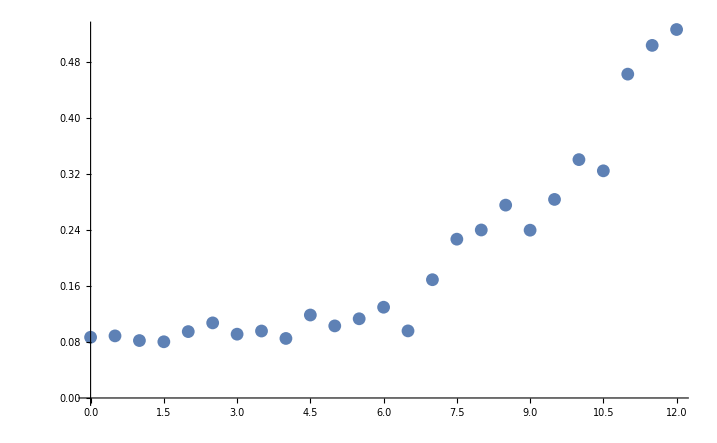

```mathematica
ListPlot[data]
```

```mathematica
data=ParallelTable[{b,Table[ecc[glauberMCcollcoords[b],3],{i,0,10}]},{b,0,12,0.5}];//AbsoluteTiming
```

{159.549,Null}

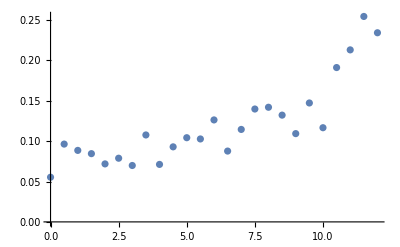

```mathematica
data=data/.{a_,b_}:>{a,Mean[b]};
ListPlot[data]
```

```mathematica
gauss[x_,x1_,y_,y1_,r_]:=Exp[-((x-x1)^2+(y-y1)^2)/(2 r^2)];
sumgauss[x_,y_,r_,collcoords_]:=Sum[gauss[x,collcoords[[i,1]],y,collcoords[[i,2]],r],{i,Length[collcoords]}];
```

```mathematica
data=ParallelTable[{b,Table[sumgauss[2,2,1.0,glauberMCcollcoords[b]],{i,0,100}]},{b,0,12,0.5}];//AbsoluteTiming
```

{206.014,Null}

```mathematica
data=data/.{a_,b_}:>{a,Mean[b]};
```

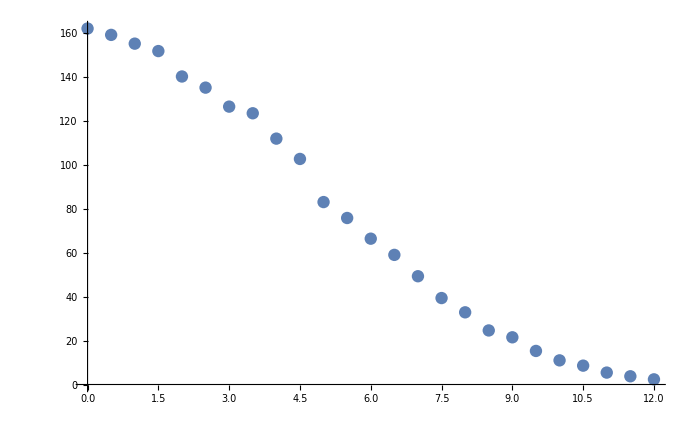

```mathematica
ListPlot[data]
```

```mathematica
endenTab[impact_,r_,n_]:=Flatten[ParallelTable[{{x,y},1/n Sum[sumgauss[x,y,r,glauberMCcollcoords[impact]],{i,1,n}]},{x,-6,6,1},{y,-6,6,1}],1]
```

```mathematica
endeninter=Interpolation[endenTab[0,0.4,1]];//AbsoluteTiming
```

{5.07077,Null}

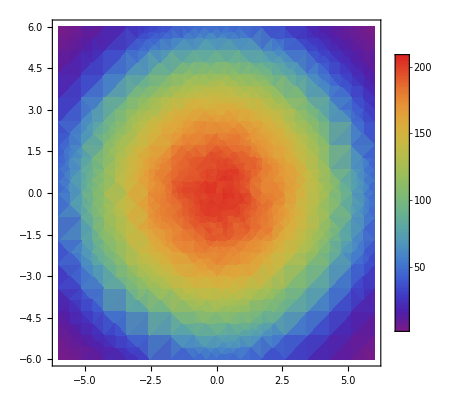

```mathematica
DensityPlot[endeninter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

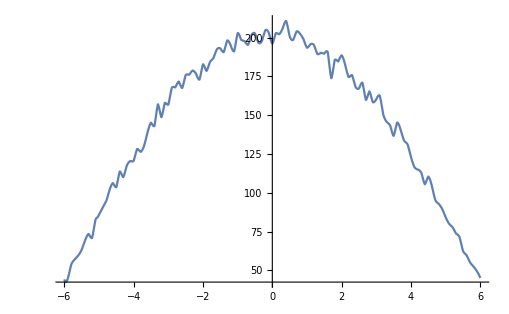

```mathematica
Plot[endeninter[x,0],{x,-6,6},PlotLegends->Automatic,PlotRange->All]
```

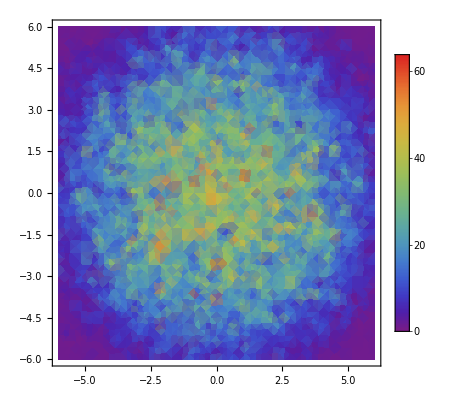

```mathematica
DensityPlot[endeninter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

```mathematica
Plot3D[endeninter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

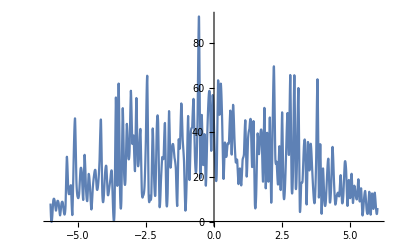

```mathematica
Plot[endeninter[x,0],{x,-6,6},PlotLegends->Automatic,PlotRange->All]
```

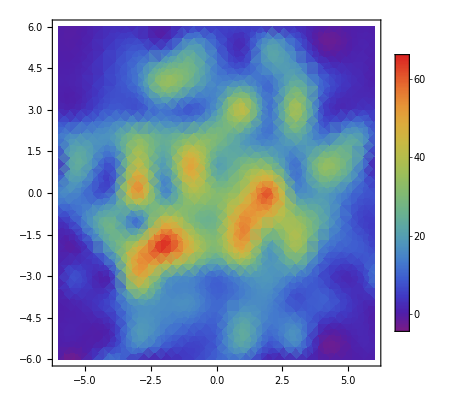

```mathematica
DensityPlot[endeninter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

```mathematica
Plot3D[endeninter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

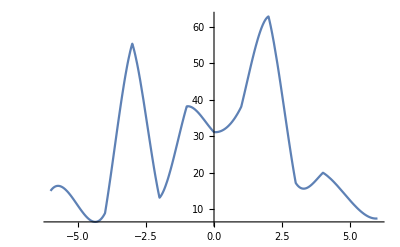

```mathematica
Plot[endeninter[x,0],{x,-6,6},PlotLegends->Automatic,PlotRange->All]
```